```mathematica
dat=Import[NotebookDirectory[]<>"toplot.dat"];
datn=Select[#,NumberQ]&/@Transpose@dat;Ordering[Length/@datn];
```

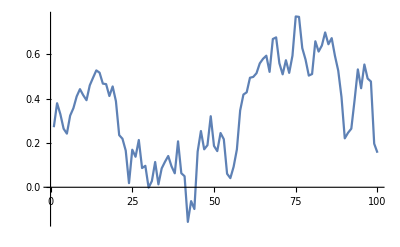

```mathematica
ListLinePlot[dat[[;;,200]],PlotRange->All]
```

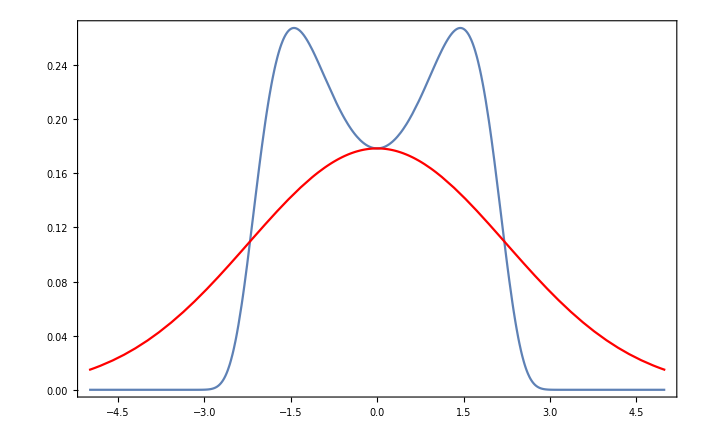

```mathematica
t=500;
a=0.1;
exp=PDF[TransformedDistribution[ArcSinh[a u],u\[Distributed]NormalDistribution[0,√t]],x];
exp2=PDF[NormalDistribution[0,a √t],x];
Quiet@Show[
Plot[exp,{x,-5,5},PlotRange->All],
Plot[exp2,{x,-5,5},PlotRange->All,PlotStyle->Red]
,PlotRange->{{-5,5},All},Frame->True,Axes->False]
```

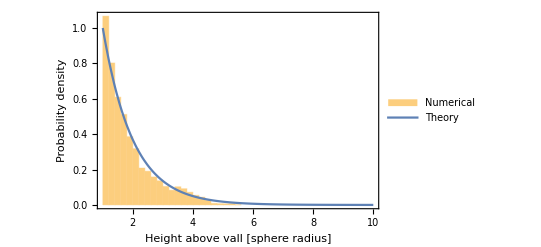

```mathematica
Show[
Histogram[
Select[dat[[;;,17]],#≠0&]
,{1,10,0.2},"PDF",ChartLegends->{"Numerical"}],
Plot[Exp[-(x-1)],{x,1,10},PlotRange->All,PlotLegends->{"Theory"}],
Frame->True,
FrameLabel-> {"Height above vall [sphere radius]","Probability density"}
]
```

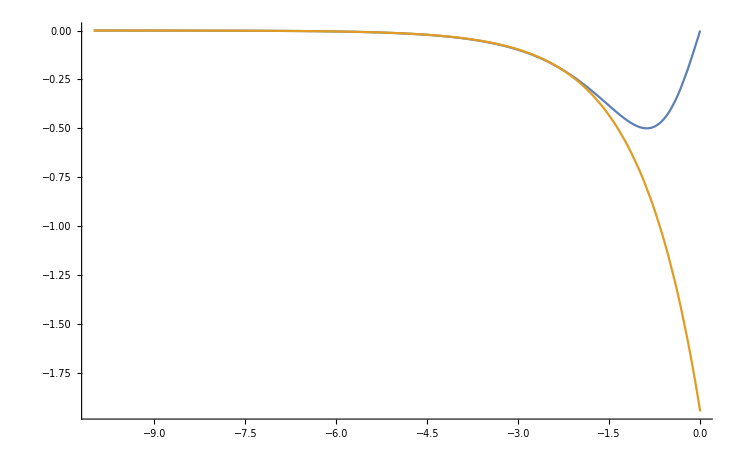

```mathematica
Plot[{Tanh[x]Sech[x],-Exp[x+2/3]},{x,-10,0},PlotRange->All]
```

```mathematica
D[Sech[x],x]//FullSimplify
```

-Sech[x] Tanh[x]

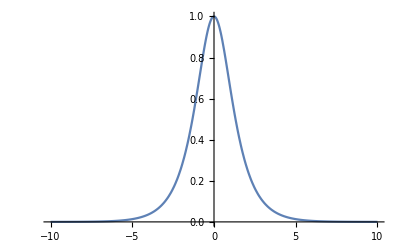

```mathematica
Plot[Sech[x],{x,-10,10}]
```

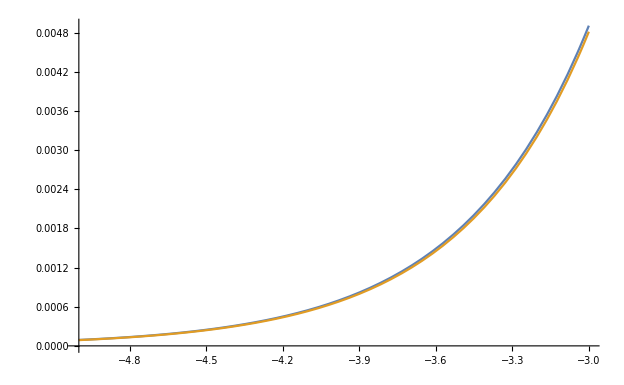

```mathematica
Plot[{-0.5 Tanh[x]Sech[x]Sech[x],0.5 Exp[x+2/3]Sech[x]},{x,-5,-3}]
```

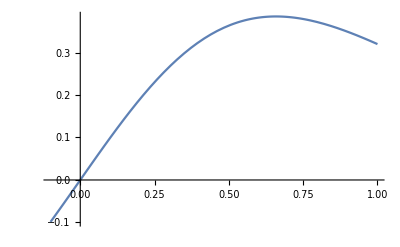

```mathematica
Plot[Tanh[x] Sech[x]^2,{x,-0.1,1}]
```

```mathematica
D[ArcSinh[x],x]/.x->0
```

1

```mathematica
D[-0.5 A^2 Tanh[x] Sech[x]^2,x,x]//FullSimplify
```

A^2 Sech[x]^2 Tanh[x] (4. Sech[x]^2-2. Tanh[x]^2)

```mathematica
-0.5 A^2 Tanh[x] Sech[x]^2/.A->0.1/.x->-1.5//ScientificForm
D[-0.5 A^2 Tanh[x] Sech[x]^2,x]/.A->0.1/.x->-1.5//ScientificForm
D[A^2 Sech[x]^2 Tanh[x] (4. Sech[x]^2-2. Tanh[x]^2),x,x]/.A->0.1/.x->-1.5//ScientificForm
```

8.17831×10^-4

1.31724×10^-3

-1.27695×10^-2

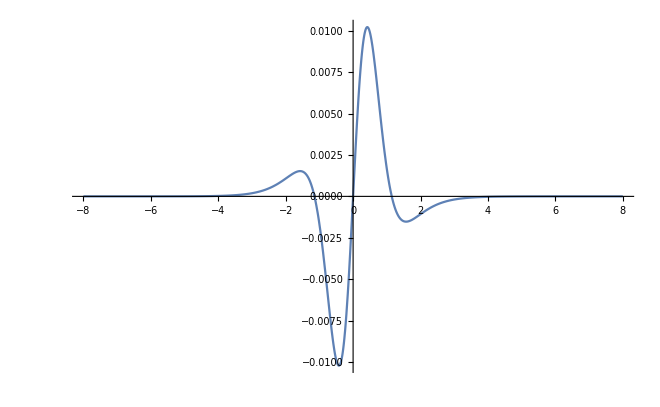

```mathematica
Plot[A^2 Sech[x]^2 Tanh[x] (4. Sech[x]^2-2. Tanh[x]^2)/.A->0.1,{x,-8,8},PlotRange->All]
```

```mathematica
me=Mean[TransformedDistribution[(dw^2-dt)^2,dw\[Distributed]NormalDistribution[w/t dt,√(dt(t-dt))]]]//FullSimplify
```

dt^2 (1+3 dt^2+dt (2-6 t)+t (-2+3 t)-(2 dt (1+3 dt-3 t) w^2)/t^2+(dt^2 w^4)/t^4)

```mathematica
Series[me,{dt,0,3}]//FullSimplify
```

(1+t (-2+3 t)) dt^2+(2-6 t+(2 (-1+3 t) w^2)/t^2) dt^3+O[dt]^4

```mathematica
Solve[(3 t^4+6 t^2 w^2+w^4)-2 ((1+3 t) (t^2+w^2)) dt==eps,dt]//FullSimplify
```

{{dt→(-eps+3 t^4+6 t^2 w^2+w^4)/(2 (1+3 t) (t^2+w^2))}}

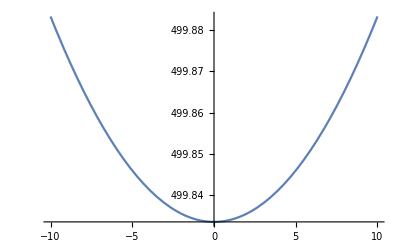

```mathematica
Plot[(-eps+3 t^4+6 t^2 w^2+w^4)/(2 (1+3 t) (t^2+w^2))/.t->1000/.eps->10,{w,-10,10}]
```

```mathematica
D[3 t^4+dt^2 (1+t (2+3 t))+6 w^2+w^4/t^4-(2 dt (1+3 t) (t^4+w^2))/t^2,t]//FullSimplify
```

```mathematica
Solve[2 (dt-2 t) (dt+3 dt t-3 t^2)+(2 dt (2+3 t) w^2)/t^3-(4 w^4)/t^5==0,t]
```

{{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,1]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,2]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,3]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,4]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,5]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,6]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,7]},{t→Root[-2 w^4+2 dt w^2 #1^2+3 dt w^2 #1^3+dt^2 #1^5+(-2 dt+3 dt^2) #1^6-9 dt #1^7+6 #1^8&,8]}}

```mathematica
expr=Sin[2Cos[#]]&@"dupa"
```

Sin[2 Cos[dupa]]